```mathematica
deq=D[Y[x,t],t]-𝒟 D[Y[x,t],{x,2}]==0;
```

```mathematica
f0[t_]:=1/2(1+t)
```

```mathematica
f1[t_]:=1/2
```

```mathematica
g0[x_]:=1/2
```

```mathematica
sol=DSolve[{
deq,
Y[0,t]==f0[t],
Y[1,t]==f1[t],
Y[x,0]==g0[x]},
Y[x,t],{x,t}]
```

{{Y[x,t]→1/2 (1+t-t x)+((-1+ⅇ^(-π^2 t 𝒟 K[1]^2)) Sin[π x K[1]])/(π^3 K[1]^3)K[1]1∞}}

```mathematica
Yf[x_,t_,d_]:=Y[x,t,d]/.sol[[1]]
```

```mathematica
Yf[x_,t_,d_]:=1/2(1+t(1-x))+∑_(k=1)^100 ((ⅇ^(-π^2 t d k^2)-1)Sin[π x k])/(π^3 k^3)
```

```mathematica
dd=0.1;
```

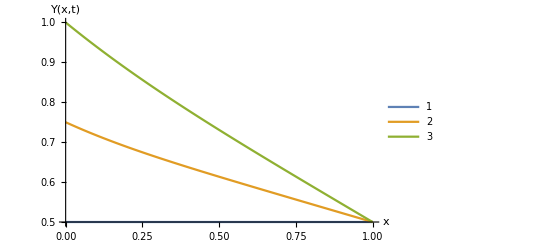

```mathematica
Plot[{Yf[x,0,dd],Yf[x,0.5,dd],Yf[x,1,dd]},{x,0,1},AxesLabel->{"x","Y(x,t)"},PlotRange->All,PlotLegends->Automatic]
```